```mathematica
Select[Keys[allGraphs5],!ConnectedGraphQ[MakeUndirected[FormulaGraphReverse2[allGraphs5[#,"colotree"]]]]&]
```

{}

```mathematica
Select[Keys[allGraphs5],!ConnectedGraphQ[MakeUndirected[FormulaGraphReverse2[allGraphs5[#,"colofour"]]]]&]
```

{}

```mathematica
Select[Keys[allGraphs5],!ConnectedGraphQ[MakeUndirected[FormulaGraphReverse2[allGraphs5[#,"colofournull"]]]]&]
```

{}

```mathematica
Select[Keys[allGraphs5],!ConnectedGraphQ[MakeUndirected[FormulaGraphReverse2[allGraphs5[#,"colofourrealnull"]]]]&]
```

{}

```mathematica
Select[Keys[allGraphs5],!ConnectedGraphQ[MakeUndirected[FormulaGraphReverse2[allGraphs5[#,"colofourgenerator"]]]]&]
```

{29487,29485,29439,29431,29413,29407,29404,29277,29271,29253,29244,29245,29196,29199,29197,28785,28783,28713,28687,28549,28525,28458,28461,28459,28434,28435,28432,27333,27325,27309,27229,27054,27085,27063,27055,27013,26982,26983,26974,26605,26599,26596,26581,26527,26500,26325,26352,26361,26355,26337,26335,26328,26326,26271,26280,26283,26275,26272,26253,26256,26254,26247,26248,26245,22842,22959,22953,22933,22873,22851,22845,22693,22639,22608,22611,22602,22113,22233,22224,22225,22207,22140,22149,22141,22125,22123,22116,22114,21991,21964,21897,21906,21907,21900,21901,21879,21882,21880,21873,21874,21871,20655,20736,20772,20775,20773,20739,20737,20695,20664,20667,20659,20656,20493,20533,20502,20503,20496,20497,20452,20421,20424,20422,20415,20416,20413,20010,20011,20008,19962,19963,19954,19935,19938,19936,19929,19930,19927,19800,19803,19794,19773,19776,19774,19767,19768,19765,19719,19722,19720,19713,19714,19711,19692,19695,19693,19686,19687,19684,9720,9801,9813,9811,9747,9759,9751,9558,9585,9595,9589,9504,8991,9099,9111,9109,9075,9073,9018,9030,9031,8994,8995,8992,8829,8856,8869,8866,8832,8833,8830,8775,8778,8779,8776,8751,8749,7533,7614,7641,7653,7645,7626,7627,7569,7561,7542,7543,7534,7371,7398,7411,7402,7380,7381,7372,7317,7326,7327,7318,7299,7291,6885,6912,6888,6889,6886,6831,6840,6841,6832,6814,6808,6805,6642,6669,6678,6681,6672,6651,6654,6652,6645,6646,6643,6588,6597,6600,6598,6591,6592,6589,6571,6565,6562,3159,3240,3267,3277,3271,3253,3250,3186,3199,3190,3168,3171,3162,2997,3033,3027,3006,3009,3000,2943,2952,2955,2946,2925,2919,2430,2511,2538,2514,2515,2512,2457,2466,2467,2458,2439,2442,2440,2433,2434,2431,2295,2304,2307,2298,2280,2271,2272,2214,2223,2226,2224,2217,2218,2215,2199,2190,2191,972,1053,1080,1056,1057,1054,999,1008,1009,1000,981,984,982,975,976,973,810,837,846,849,840,819,822,820,813,814,811,765,768,766,738,741,739,327,325,279,271,253,247,244,117,111,93,84,85,36,39,37}

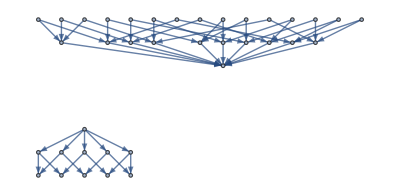

```mathematica
GraphUnion[Map[ChangeSymbol[#,"v"]&,allGraphs5[lambdaKey,"colofourgenerator"]],FormulaGraphReverse3[allGraphs5[lambdaKey,"colofournull"]]]
```

```mathematica
With[{gen=Map[ChangeSymbol[#,"v"]&,ListofVars[allGraphs5[lambdaKey,"colofourgenerator"]]],
fake=Map[ChangeSymbol[#,"v"]&,ListofVars[allGraphs5[lambdaKey,"colofournull"]]]
},
Intersection[gen,fake]
]
```

{v13x24x5,v13x25x4,v14x25x3,v14x2x35,v1x24x35}

```mathematica
Handle[k_]:=ShowGraph5Least[k]->With[{gen=Map[ChangeSymbol[#,"v"]&,ListofVars[allGraphs5[k,"colofourgenerator"]]],
fake=Map[ChangeSymbol[#,"v"]&,ListofVars[allGraphs5[k,"colofournull"]]]
},
FormulaGraphReverse2[Intersection[gen,fake]]
]
```

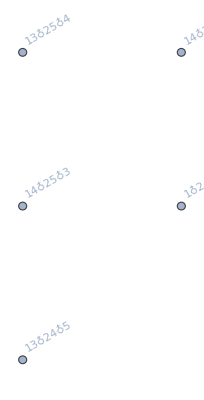
-Graphics-206653→-Graphics-

```mathematica
Handle[lambdaKey]
```

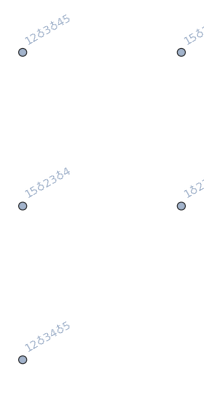
-Graphics-88595→-Graphics-

```mathematica
Handle[starKey]
```

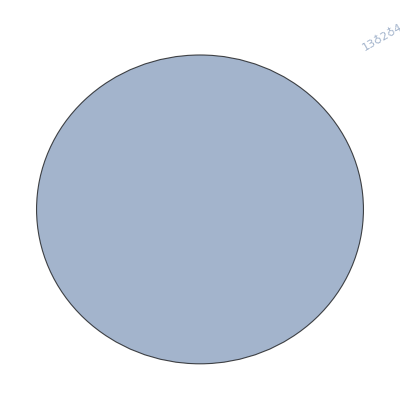
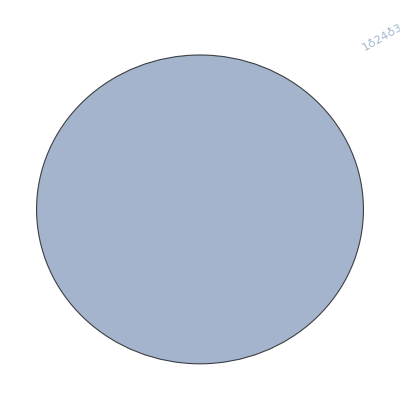
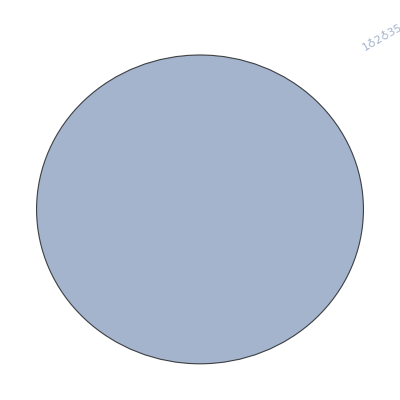
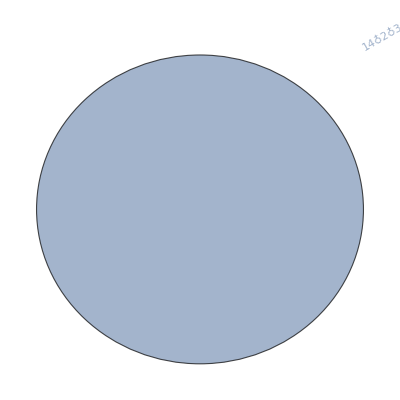
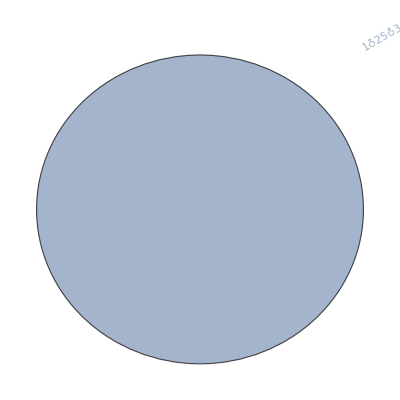
{-Graphics-360850→-Graphics-,-Graphics-296050→-Graphics-,-Graphics-295270→-Graphics-,-Graphics-317110→-Graphics-,-Graphics-295510→-Graphics-}

```mathematica
Table[Handle[k],{k,quads}]
```

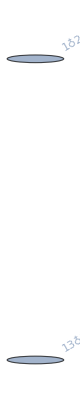
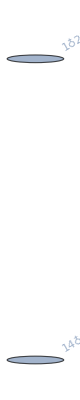
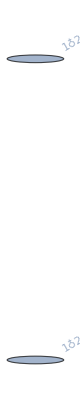
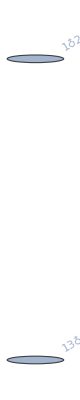
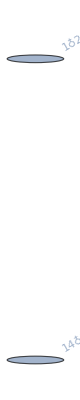
{-Graphics-361660→-Graphics-,-Graphics-317380→-Graphics-,-Graphics-296080→-Graphics-,-Graphics-361120→-Graphics-,-Graphics-317140→-Graphics-}

```mathematica
Table[Handle[k],{k,alfa1s}]
```